```mathematica
Needs["Polytopes`"];
```

SetDelayed::write: Tag Area in Area[polygon_] is Protected.

UpSet::write: Tag Tetrahedron in Volume[Tetrahedron] is Protected.

UpSet::write: Tag Tetrahedron in Dual[Tetrahedron] is Protected.

UpSet::write: Tag Tetrahedron in Schlafli[Tetrahedron] is Protected.

General::stop: Further output of UpSet::write will be suppressed during this calculation.

TagSetDelayed::write: Tag Cube in NumberOfVertices[Cube] is Protected.

TagSetDelayed::write: Tag Cube in NumberOfEdges[Cube] is Protected.

TagSetDelayed::write: Tag Cube in NumberOfFaces[Cube] is Protected.

General::stop: Further output of TagSetDelayed::write will be suppressed during this calculation.

TagSet::write: Tag Octahedron in Vertices[Octahedron] is Protected.

TagSet::write: Tag Octahedron in Faces[Octahedron] is Protected.

TagSet::write: Tag Dodecahedron in Vertices[Dodecahedron] is Protected.

General::stop: Further output of TagSet::write will be suppressed during this calculation.

```mathematica
polygon=Vertices[Dodecagon]
```

{{(√3)/2,1/2},{1/2,(√3)/2},{0,1},{-1/2,(√3)/2},{-(√3)/2,1/2},{-1,0},{-(√3)/2,-1/2},{-1/2,-(√3)/2},{0,-1},{1/2,-(√3)/2},{(√3)/2,-1/2},{1,0}}

```mathematica
lines=MapThread[{#1, #2}.RotationMatrix[-π/8]&, {polygon, Append[polygon[[2;;]],polygon[[1]]]}];
```

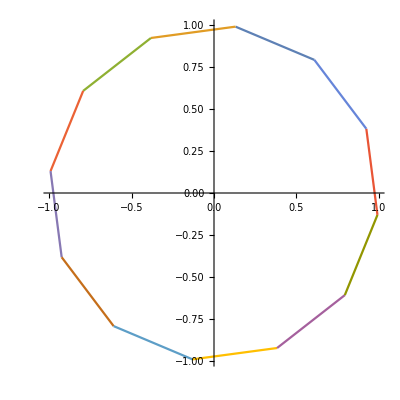

```mathematica
ListLinePlot[lines, AspectRatio->1]
```

```mathematica
(* point to line distance: *)
(*
Calculate distance from point to line.
Helper for calculating nearest point to geofence.
Reference:https://stackoverflow.com/questions/849211/shortest-distance-between-a-point-and-a-line-segment
      @return {distance,yy,xx} where yy,xx are the coordinates of the nearest point on the line,
to our (lat,lon) point.*)
nearestPointToLine[lat_,lon_,p1_,p2_,overshoot_]:= Module[{x1,y1,x2,y2,xx,yy, a, b,c, d, dot, lenSq, param},
 {
x1=p1[[1]];
y1=p1[[2]];
 x2=p2[[1]];
 y2=p2[[2]];
 a=lat-y1;
 b=lon-x1;
 c=y2-y1;
 d=x2-x1;
 dot=a c+b d;
 lenSq=c c+d d;
 param=-1.;
If[lenSq≠0,param=dot/lenSq,{}];

If [param<0,xx=x1;yy=y1,If[param>1 ,xx=x2;yy=y2, xx=x1+param d;yy=y1+param c]];

 dx=xx-lon;
 dy=yy-lat;
(* Overshoot the perimeter point towards the other side of the line *)  theta=ArcTan[dx,dy];
xx+=overshoot Cos[theta];
yy+=overshoot Sin[theta];
{√(dx^2+dy^2),{xx, yy}}}]
```

```mathematica
point={-1,-1/2};
overshoot=1/10;
```

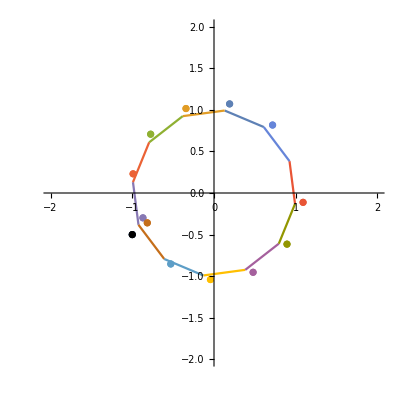

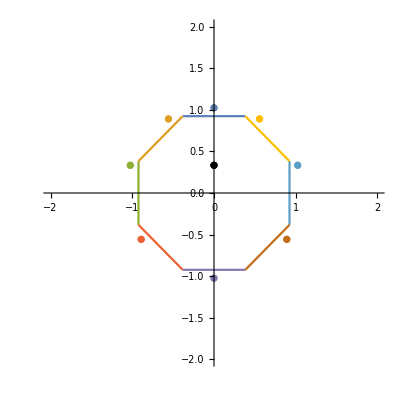

```mathematica
nearest =Flatten[nearestPointToLine[point[[2]], point[[1]],#[[1]], #[[2]],overshoot]&/@lines,1]//N;
Show[ListPlot[{#[[2]]}&/@nearest, {PlotRange-> {{-2,2},{-2,2}},AspectRatio->1}], ListLinePlot[lines],ListPlot[{Style[point, Black]}]]
```